```mathematica
Clear["Global`*"];
SetDirectory[NotebookDirectory[]<>"\\MethodsODE\\OutputData\\"];
```

```mathematica
"C:\\Users\\gerce\\WORK DIRECTORY\\NumericalMethodsLABS\\MethodsODE\\OutputData"
```

C:\Users\gerce\WORK DIRECTORY\NumericalMethodsLABS\MethodsODE\OutputData

Метод Эйлера Явный

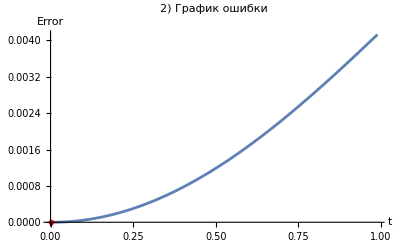
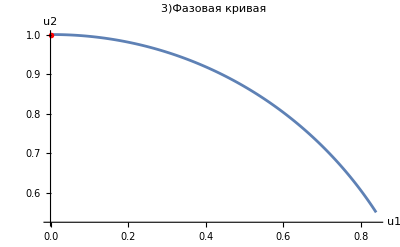
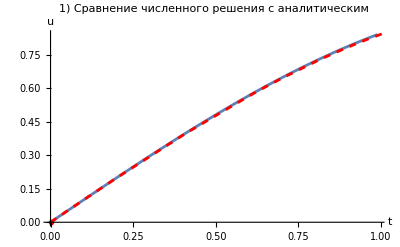
Null -Graphics- -Graphics- -Graphics-

```mathematica
(* Модуль для отрисоввки графиков теста 0 (маятник)*)
TEST0[solve_, data_, text_ : " ", ifhplot_ : False]  := Module[{plotsolve1, plot1data1,plot2data1, ploterror1,plot1, plot2, plot3},
plotsolve1= Plot[solve,{t,0,10},PlotStyle->{Red,Dashed}];

plot1data1= ListPlot[Table[{data[[i]][[1]],data[[i]][[2]]},{i,1,Length[data]}],Joined->True];

plot2data1=ListPlot[Table[{data[[i]][[2]],data[[i]][[3]]},{i,1,Length[data]}],Joined->True,AxesLabel->{"u1", "u2"}];

ploterror1 = ListPlot[Table[{data[[i]][[1]], Abs[(solve/.t->data[[i]][[1]])-data[[i]][[2]]]}, {i,1,Length[data]}], Joined->True,AxesLabel->{"t", "ERROR"}];
Print[text];
plot1 = Show[plot1data1, Graphics[{Red,PointSize[0.01],Point[{data[[1]][[1]],data[[1]][[2]]}]}],plotsolve1,AxesLabel->{"t", "u"},AxesStyle->Arrowheads[0.03], PlotLabel -> "1) Сравнение численного решения с аналитическим",LabelStyle -> Below,ImageSize->400];
plot2 = Show[ploterror1, Graphics[{Red,PointSize[0.01],Point[{data[[1]][[1]],data[[1]][[2]]}]}],AxesLabel->{"t", "Error"},AxesStyle->Arrowheads[0.03], PlotLabel-> "2) График ошибки",ImageSize->400];

plot3 = Show[plot2data1,Graphics[{Red,PointSize[0.01],Point[{data[[1]][[2]],data[[1]][[3]]}]}], AxesStyle->Arrowheads[0.03], PlotLabel-> "3)Фазовая кривая", ImageSize->400];
If[ifhplot, Show[ListPlot[Table[{data[[i]][[1]], Abs[data[[i]][[1]]-data[[i+1]][[1]]]}, {i,1,Length[data]-1}], Joined->True,AxesLabel->{"t", "h"},  ImageSize->400]]]
plot1
plot2
plot3

(*Show[GraphicsRow[{plot1, plot2, plot3}, ImageSize->1000,Spacings->{0,0}], PlotLabel->text, LabelStyle->"Subsection"]*)

];

(* Заданные условия *)
m = 1; k = 1; 
u10=0;u20=1;
solve1 = DSolve[{y''[t]+k/m y[t]==0,y[0]==u10,y'[0]==u20},y[t],t][[1]][[1]][[2]];
data1=Import["f0-eulersimple-0","Table"];
data2=Import["f0-eulerImplicit-0","Table"];
data3=Import["f0-simScheme-0","Table"];
data4=Import["f0-rungekutta2-0","Table"];
data5=Import["f0-rungekutta2auto-0","Table"];
data6=Import["f0-rungekutta4-0","Table"];
data7=Import["f0-rungekutta4auto-0","Table"];
data8=Import["f0-adams4-0","Table"];
data9=Import["f0-predict4-0","Table"];

TEST0[solve1, data1, "Метод Эйлера Явный"]
```

Метод Эйлера Неявный

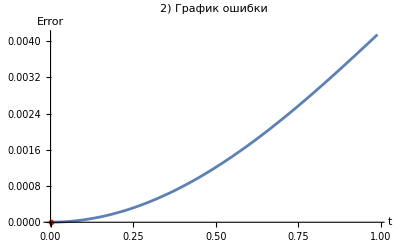
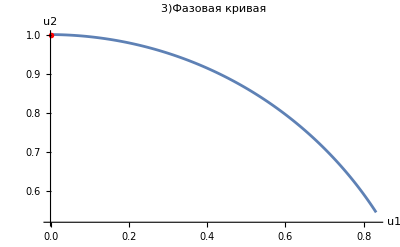
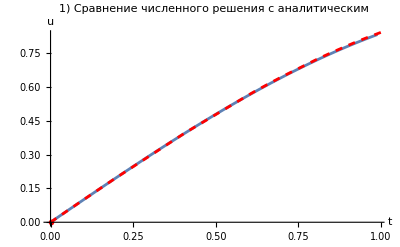
Null -Graphics- -Graphics- -Graphics-

```mathematica
TEST0[solve1, data2, "Метод Эйлера Неявный"]
```

Метод Симметричной схемы

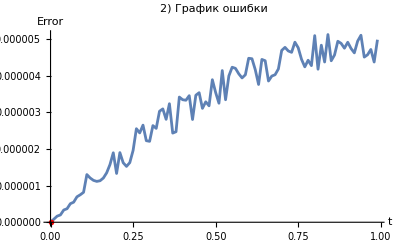
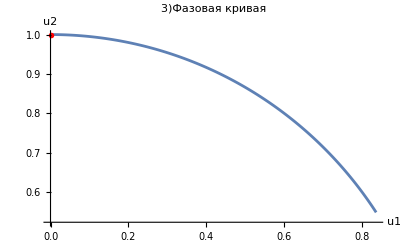
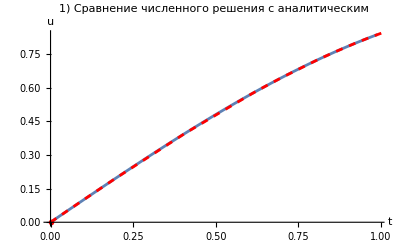
Null -Graphics- -Graphics- -Graphics-

```mathematica
TEST0[solve1, data3, "Метод Симметричной схемы"]
```

Метод Рунге-Кутты двустадийный

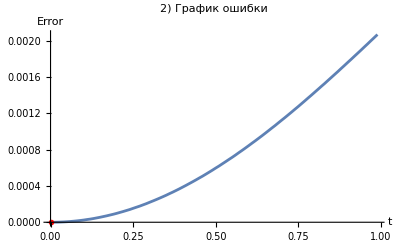
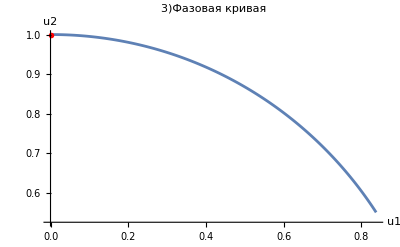
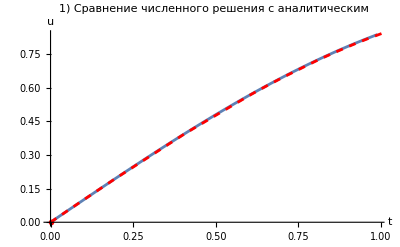
Null -Graphics- -Graphics- -Graphics-

```mathematica
TEST0[solve1, data4, "Метод Рунге-Кутты двустадийный"]
```

Метод Рунге-Кутты двустадийный с Автоматическим шагом

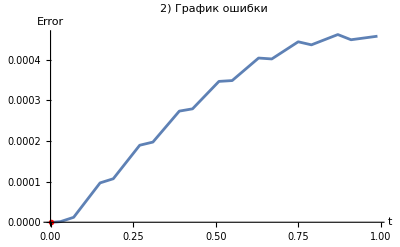
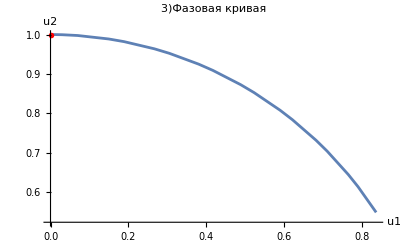
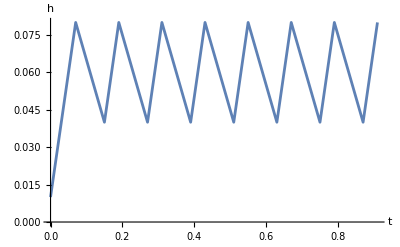
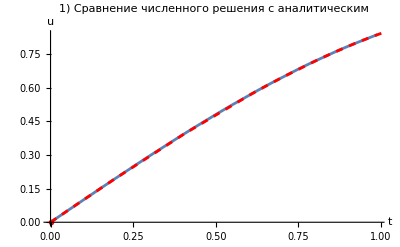

```mathematica
TEST0[solve1, data5, "Метод Рунге-Кутты двустадийный с Автоматическим шагом", True]
```

Метод Рунге-Кутты четрехстадийный

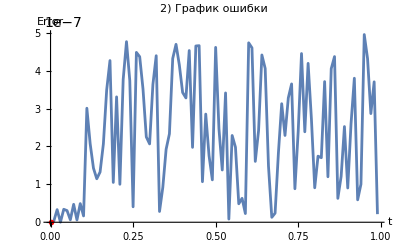
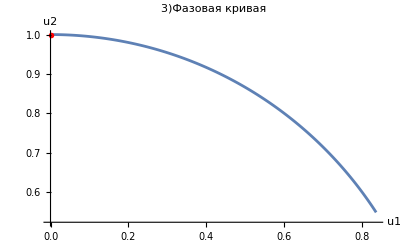
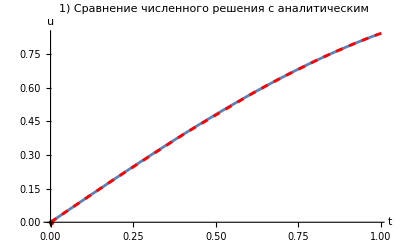
Null -Graphics- -Graphics- -Graphics-

```mathematica
TEST0[solve1, data6, "Метод Рунге-Кутты четрехстадийный"]
```

Метод Рунге-Кутты четрехстадийный с Автоматическим шагом

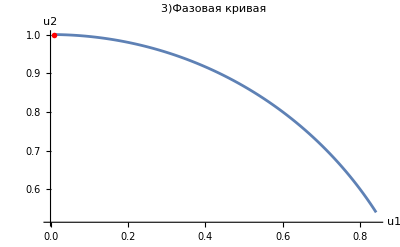
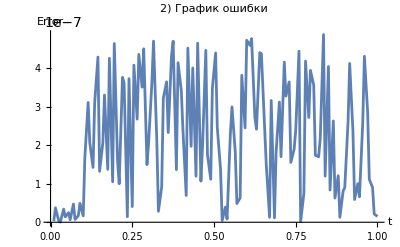
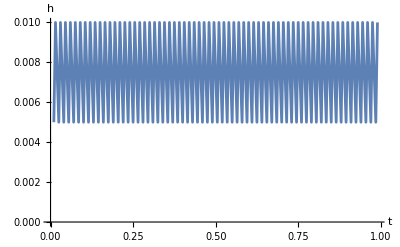
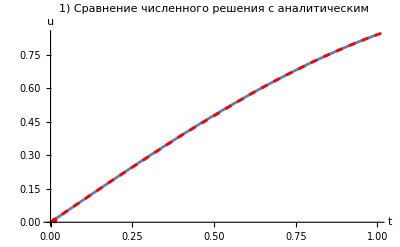

```mathematica
TEST0[solve1, data7, "Метод Рунге-Кутты четрехстадийный с Автоматическим шагом", True]
```

Метод Адамса-Башфорта

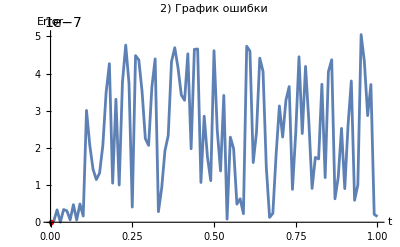
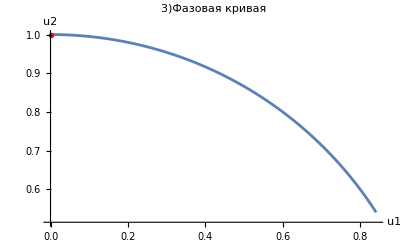
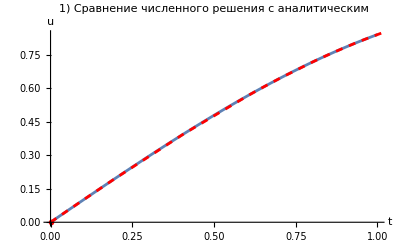
Null -Graphics- -Graphics- -Graphics-

```mathematica
TEST0[solve1, data8, "Метод Адамса-Башфорта"]
```

```mathematica
TEST0[solve1, data9, "Метод Прогноз-Коррекция"]
```

Метод Прогноз-Коррекция

Null -Graphics- -Graphics- -Graphics-